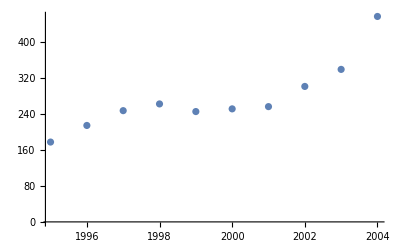

```mathematica
(* Задача 1 *)
data={
{1995,178},
{1996,215},
{1997,248},
{1998,263},
{1999,246},
{2000,252},
{2001,257},
{2002,302},
{2003,340},
{2004,458}};
dataPlot=ListPlot[data]
```

```mathematica
(* A third degree polynomial might be close to the real curve, so we will use least squares with it *)
polyDeg=3;
BasisForPolynomials[n_?NumberQ]:=Table[With[{k=k},#^k&],{k,0,n}]
polyBasis=BasisForPolynomials[polyDeg];
q=Table[Subscript[x, i],{i,0,polyDeg}];
```

```mathematica
(* а) *)
GramMatrix[basis_?ListQ, scalarProduct_]:=Table[Table[scalarProduct[basis⟦i⟧,basis⟦j⟧],{j,1,Length@basis}],{i,1,Length@basis}]
dataScalarProduct[f_,g_]:=Sum[f@data⟦i⟧⟦1⟧ g@data⟦i⟧⟦1⟧,{i,1,Length@data}]
A=Table[Table[polyBasis⟦j⟧@data⟦i⟧⟦1⟧,{j,1,Length@polyBasis}],{i,1,Length@data}];
LinearSolve[Transpose[A].A,Transpose[A].(#⟦2⟧&/@data)]

B=GramMatrix[polyBasis,dataScalarProduct];
LinearSolve[B,
Table[
Sum[data⟦j⟧⟦2⟧polyBasis⟦i⟧@data⟦j⟧⟦1⟧,{j,1,Length@data}],
{i,1,Length@polyBasis}]
]
```

{-27399314120212/2145,98694339589/5148,-16458527/1716,4117/2574}

{-27399314120212/2145,98694339589/5148,-16458527/1716,4117/2574}

{x_0→-27399314120212/2145,x_1→98694339589/5148,x_2→-16458527/1716,x_3→4117/2574}

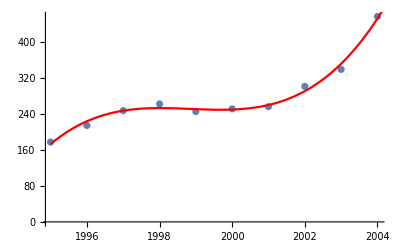

```mathematica
(* б) *)
(* {mininimum,minCoeffs}=Minimize[Sum[(q . ((#@data⟦i⟧⟦1⟧)&/@polyBasis )- data⟦i⟧⟦2⟧)^2,{i,1,Length@data}],q];
N@minCoeffs
polynomialPlot=Plot[(q/.minCoeffs).((#@x)&/@polyBasis),{x,data⟦1⟧⟦1⟧,data⟦-1⟧⟦1⟧+1},PlotStyle->Red]; *)
{mininimum,minCoeffs}=Minimize[Sum[(q . Through[polyBasis [data⟦i⟧⟦1⟧]]- data⟦i⟧⟦2⟧)^2,{i,1,Length@data}],q];
minCoeffs
polynomialPlot=Plot[(q/.minCoeffs).(Through[polyBasis[x]]),{x,data⟦1⟧⟦1⟧,data⟦-1⟧⟦1⟧+1},PlotStyle->Red]; 
Show[{dataPlot,polynomialPlot}]
```

```mathematica
(* в) *)
A=Table[Table[polyBasis⟦j⟧@data⟦i⟧⟦1⟧,{j,1,Length@polyBasis}],{i,1,Length@data}];
(* N because Mathematica is stupid *)
{U,Σ,V}=N@SingularValueDecomposition@A;
safeReciprocal[ξ_?NumberQ]:=If[ξ≠0,1/ξ,0]
(*Θ=safeReciprocal/@#&/@Σ*)
Θ=Map[safeReciprocal,Σ,{2}];
(*Θ=DiagonalMatrix@TakeWhile[safeReciprocal/@Diagonal@Σ,#≠0&];*)
Api=V.Transpose@Θ.Transpose@U;
Api.(#[[2]]&/@data)
```

{-1.27736×10^10,1.91714×10^7,-9591.22,1.59946}

```mathematica
(* Задача 2 *)
image=ExampleData[{"TestImage","Lena"}];
ColorCombine[ColorSeparate@image, "RGB"];
{red, green,blue} = ImageData/@ColorSeparate@image;
gray=ImageData@ColorConvert[image,"Grayscale"];
```

```mathematica
(*ImageData@red
SingularValueDecomposition[ImageData@ColorConvert[red,"Grayscale"]]*)
compressImage[imageData_,ε_ ]:=(
{U,Σ,V} = SingularValueDecomposition@imageData;
singularValues =Diagonal@Σ;
compressedValues=TakeWhile[singularValues,#≥ε&];
If[Length@compressedValues ==0,
Return[
ConstantArray[0,Dimensions@imageData]
];
];
compressedU=Transpose@Take[Transpose@U,Length@compressedValues];
compressedVt=Take[Transpose@V,Length@compressedValues];
compressedU.DiagonalMatrix[compressedValues].compressedVt
)
```

```mathematica
redComp=compressImage[red,5];
greenComp=compressImage[green,5];
blueComp=compressImage[blue,5];
imageComp=ColorCombine[Image/@{redComp,greenComp,blueComp},"RGB"];
GraphicsGrid[{{image,imageComp}}]
```

-Graphics-

```mathematica
GraphicsGrid[{{Image@gray,Image@compressImage[gray,10]}}]
```

-Graphics-

```mathematica
compressImage[red,1]
```

{{0.882642,0.882642,0.876183,506,0.896831,0.854607,0.775069},510,{1}}
 |  |  |  |

-Graphics-

-Graphics-

-Graphics-